# Smooth code for VTI

```mathematica
Clear["Global`*"]
```

```mathematica
param={v01->1.5,v02->2,vn1->1.5,vn2->2,eta1->0,eta2->0,alfa->4,dz->2}
```

{v01→1.5,v02→2,vn1→1.5,vn2→2,eta1→0,eta2→0,alfa→4,dz→2}

```mathematica
z0=3
```

3

## V0 smoothing

## unsmooth model for V0

## smoothed model

```mathematica
a=1/v01/.param;
```

```mathematica
b=1/v02/.param;
```

```mathematica
K=Piecewise[{{a,x≤z0},{b,x≥z0}}]/.param
```

Piecewise[{{0.666667, x≤3}, {1/2, x≥3}, {0, True}}]

```mathematica
m1:=a/;x≤z0
```

```mathematica
m1:=b/;x≥z0
```

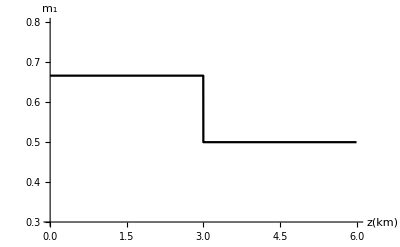

```mathematica
L1=Plot[m1,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0.3},PlotRange->{{0,6},{0.3,0.8}},AxesLabel->{Style["z(km)",FontSize->15],Style["m_1",FontSize->15]}]
```

```mathematica
F1=(Integrate[K*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

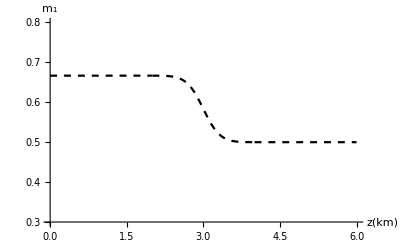

```mathematica
L2=Plot[F1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0.3},PlotRange->{{0,6},{0.3,0.8}},PlotRange->All,AxesLabel->{Style["z(km)",FontSize->15],Style["m_1",FontSize->15]}]
```

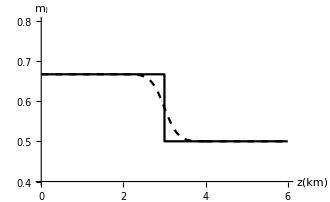

```mathematica
Show[{L1,L2},AxesOrigin->{0,0.4},PlotRange->{{0,6},{0.4,0.8}},AxesLabel->{Style["z(km)",FontSize->15],Style["m_j",FontSize->15]}]
```

```mathematica
S1=N[Integrate[a-F1,{z,z0-dz/2/.param,z0}]];
```

```mathematica
S2=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-2,z0+2}]/.param];
```

```mathematica
A1=N[S1/S2];
```

```mathematica
CP=A1*E^(-alfa*(z+dz-z0)^2)/.param;
```

```mathematica
FF1=F1+CP;
```

```mathematica
L3=Plot[FF1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0.3},PlotRange->{{0,6},{0.3,0.8}},AxesLabel->{Style["z(km)",FontSize->20],Style["m_1",FontSize->20]}];
```

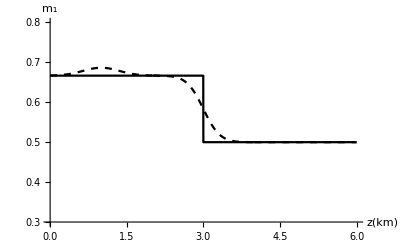

```mathematica
Show[{L1,L3},AxesOrigin->{0,0.3},PlotRange->{{0,6},{0.3,0.8}}]
```

```mathematica
CPP=A1*E^(-alfa*(z-dz-z0)^2)/.param;
```

```mathematica
M1=Simplify[F1-CPP+CP];
```

```mathematica
L4=Plot[M1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

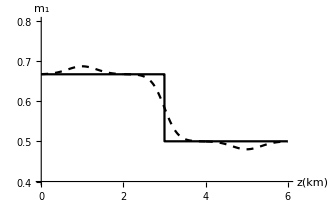

```mathematica
Show[{L1,L4},AxesOrigin->{0,0.4},PlotRange->{{0,6},{0.4,0.8}},AxesLabel->{Style["z(km)",FontSize->15],Style["m_1",FontSize->15]}]
```

```mathematica
(*HeavisideTheta*)
```

```mathematica
LL3=Plot[FF1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0.3},PlotRange->{{0,6},{0.3,0.8}},AxesLabel->{Style["z(km)",FontSize->20],Style["m_j",FontSize->20]}];
```

```mathematica
LL4=Plot[M1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

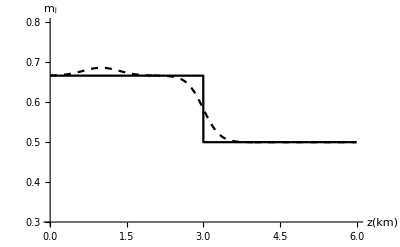

```mathematica
Show[{L1,LL3},AxesOrigin->{0,0.3},PlotRange->{{0,6},{0.3,0.8}},AxesLabel->{Style["z(km)",FontSize->15],Style["m_j",FontSize->15]}]
```

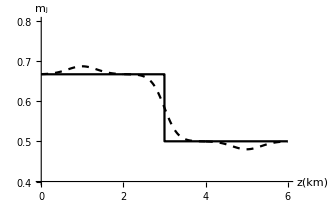

```mathematica
Show[{L1,LL4},AxesOrigin->{0,0.4},PlotRange->{{0,6},{0.4,0.8}},AxesLabel->{Style["z(km)",FontSize->15],Style["m_j",FontSize->15]}]
```

## Vn smoothing

## smoothed model

```mathematica
a1=vn1^2/v01/.param;
```

```mathematica
b1=vn2^2/v02/.param;
```

```mathematica
K1=Piecewise[{{a1,x≤z0},{b1,x≥z0}}];
```

## unsmooth model for V0

```mathematica
m2:=a1/;x≤z0;
```

```mathematica
m2:=b1/;x≥z0;
```

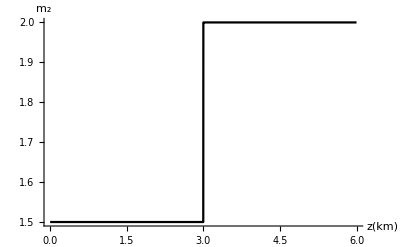

```mathematica
Ln1=Plot[m2,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["z(km)",FontSize->20],Style["m_2",FontSize->20]}]
```

```mathematica
Fn1=(Integrate[K1*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
Ln2=Plot[Fn1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
Sn1=N[Integrate[Fn1-a1,{z,z0-dz/2/.param,z0}]];
```

```mathematica
Sn2=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-2,z0+2}]/.param];
```

```mathematica
An1=N[Sn1/Sn2];
```

```mathematica
CPn=An1*E^(-alfa*(z+dz-z0)^2)/.param;
```

```mathematica
FFn1=Fn1-CPn;
```

```mathematica
Ln3=Plot[FFn1,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

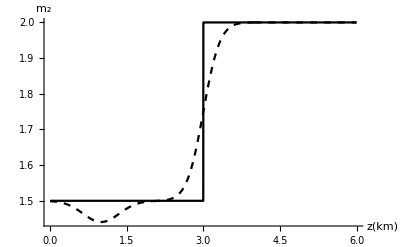

```mathematica
Show[{Ln1,Ln3},AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
CPPn=An1*E^(-alfa*(z-dz-z0)^2)/.param;
```

```mathematica
M2=Simplify[Fn1-CPn+CPPn];
```

```mathematica
Ln4=Plot[M2,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

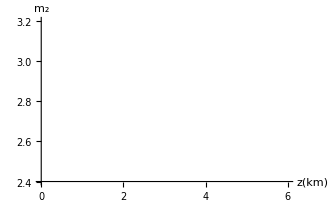

```mathematica
Show[{Ln1,Ln4},AxesOrigin->{0,2.4},PlotRange->{{0,6},{2.4,3.2}},AxesLabel->{Style["z(km)",FontSize->15],Style["m_2",FontSize->15]}]
```

## eta smoothing

## composite param

```mathematica
a2=vn1^4*(1+8*eta1)/v01/.param;
```

```mathematica
b2=vn2^4*(1+8*eta2)/v02/.param;
```

```mathematica
K2=Piecewise[{{a2,x≤z0},{b2,x≥z0}}]
```

Piecewise[{{3.375, x≤3}, {8, x≥3}, {0, True}}]

## unsmooth model for m3

```mathematica
m3:=a2/;x≤z0;
```

```mathematica
m3:=b2/;x≥z0;
```

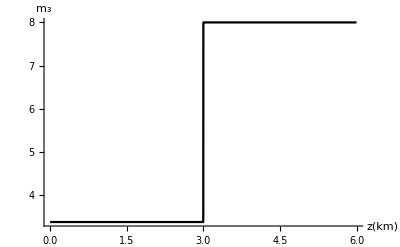

```mathematica
L1e=Plot[m3,{x,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["z(km)",FontSize->20],Style["m_3",FontSize->20]}]
```

```mathematica
Fn1e=(Integrate[K2*E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/(Integrate[E^(2*(x-z0)^2),{x,z-dz/2,z+dz/2},Assumptions->Element[{z-dz/2,z+dz/2},Reals]])/.param;
```

```mathematica
Ln2e=Plot[Fn1e,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All];
```

```mathematica
Sn1e=N[Integrate[Fn1e-a2,{z,z0-dz/2/.param,z0}]];
```

```mathematica
Sn2e=N[Integrate[E^(-alfa*(x-z0)^2),{x,z0-2,z0+2}]/.param];
```

```mathematica
An1e=N[Sn1e/Sn2e];
```

```mathematica
CPe=An1e*E^(-alfa*(z+dz-z0)^2)/.param;
```

```mathematica
FFn1e=Fn1e-CPe;
```

```mathematica
Ln3e=Plot[FFn1e,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["z(km)",FontSize->20],Style["m_3",FontSize->20]}];
```

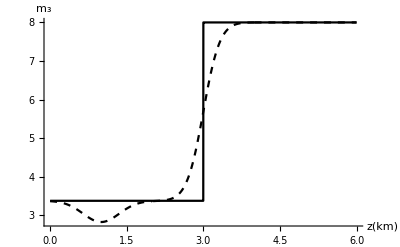

```mathematica
Show[{L1e,Ln3e},AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["z(km)",FontSize->20],Style["m_3",FontSize->20]}]
```

```mathematica
CPPne=An1e*E^(-alfa*(z-dz-z0)^2)/.param;
```

```mathematica
M3=Simplify[Fn1e-CPe+CPPne];
```

```mathematica
Ln4e=Plot[M3,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["z(km)",FontSize->20],Style["m_3",FontSize->20]}];
```

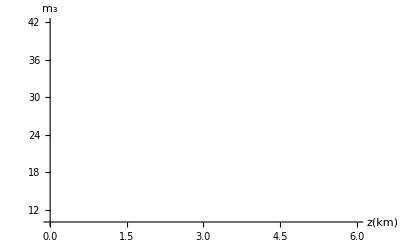

```mathematica
Show[{L1e,Ln4e},AxesOrigin->{0,10},PlotRange->{{0,6},{10,42}},AxesLabel->{Style["z(km)",FontSize->15],Style["m_3",FontSize->15]}]
```

## convert to the model parameters

```mathematica
V0=Simplify[1/M1];
```

```mathematica
Vnmo=Simplify[Sqrt[M2/M1]];
```

```mathematica
ETA=Simplify[(((M3*M1)/(M2^2))-1)/8];
```

## unsmoothed model parameters

```mathematica
vel1:=v01/;z≤z0;
```

```mathematica
vel1:=v02/;z≥z0;
```

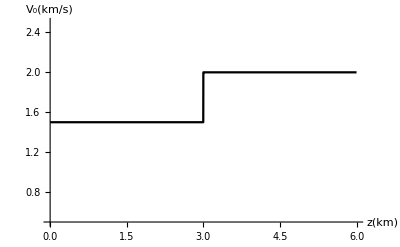

```mathematica
p10=Plot[vel1/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0.5},PlotRange->{{0,6},{0.5,2.5}},AxesLabel->{Style["z(km)",FontSize->20],Style["V_0(km/s)",FontSize->20]}]
```

```mathematica
p1=Plot[V0,{z,0,6},PlotStyle->Directive[Red],AxesOrigin->{0,0},PlotRange->All];
```

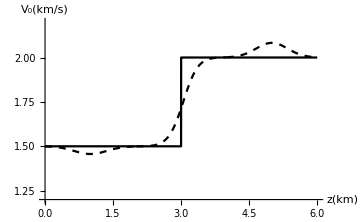

```mathematica
Show[{p10,p1},AxesOrigin->{0,1.2},PlotRange->{{0,6},{1.2,2.2}},AxesLabel->{Style["z(km)",FontSize->15],Style["V_0(km/s)",FontSize->15]}]
```

```mathematica
veln1:=vn1/;z≤z0;
```

```mathematica
veln1:=vn2/;z≥z0;
```

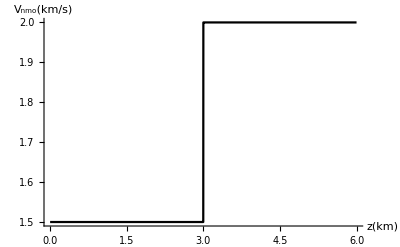

```mathematica
p20=Plot[veln1/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["z(km)",FontSize->20],Style["V_nmo(km/s)",FontSize->20]}]
```

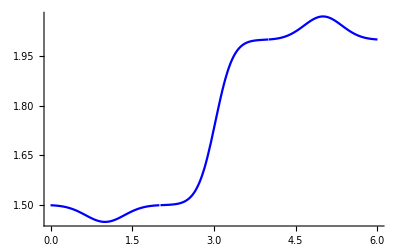

```mathematica
p2=Plot[Vnmo,{z,0,6},PlotStyle->Directive[Blue],AxesOrigin->{0,0},PlotRange->All]
```

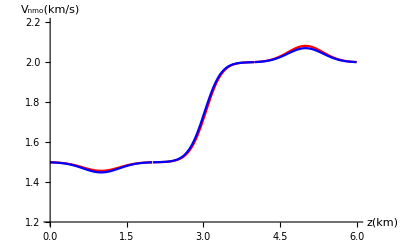

```mathematica
Show[{p1,p2},AxesOrigin->{0,1.2},PlotRange->{{0,6},{1.2,2.2}},AxesLabel->{Style["z(km)",FontSize->15],Style["V_nmo(km/s)",FontSize->15]}]
```

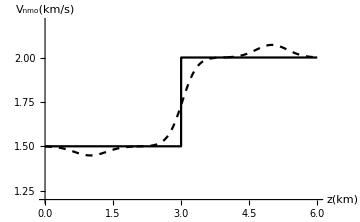

```mathematica
Show[{p20,p2},AxesOrigin->{0,1.2},PlotRange->{{0,6},{1.2,2.2}},AxesLabel->{Style["z(km)",FontSize->15],Style["V_nmo(km/s)",FontSize->15]}]
```

```mathematica
ET1:=eta1/;z≤z0;
```

```mathematica
ET1:=eta2/;z≥z0;
```

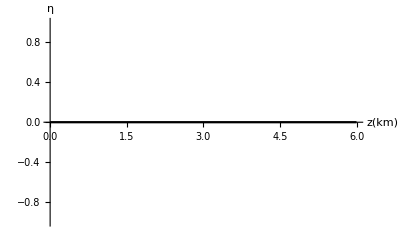

```mathematica
p30=Plot[ET1/.param,{z,0,6},PlotStyle->Black,AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["z(km)",FontSize->20],Style["η",FontSize->20]}]
```

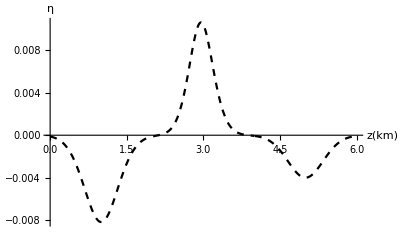

```mathematica
p3=Plot[ETA,{z,0,6},PlotStyle->Directive[Dashed,Black],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["z(km)",FontSize->20],Style["η",FontSize->20]}]
```

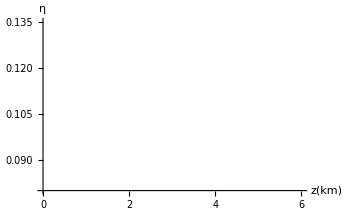

```mathematica
Show[{p30,p3},AxesOrigin->{0,0.08},PlotRange->{{0,6},{0.08,0.135}},AxesLabel->{Style["z(km)",FontSize->15],Style["η",FontSize->15]}]
```

```mathematica
Xp=Sum[(0.001*p Vnmo^2)/(V0 (1-2 ETA p^2 Vnmo^2)^(3/2) √(1-(1+2 ETA) p^2 Vnmo^2)),{z,0,6,0.001}];
```

```mathematica
Tp=Sum[(0.001*((1-2 ETA p^2 Vnmo^2)^2+2ETA*p^4Vnmo^4))/(V0 (1-2 ETA p^2 Vnmo^2)^(3/2) √(1-(1+2 ETA) p^2 Vnmo^2)),{z,0,6,0.001}];
```

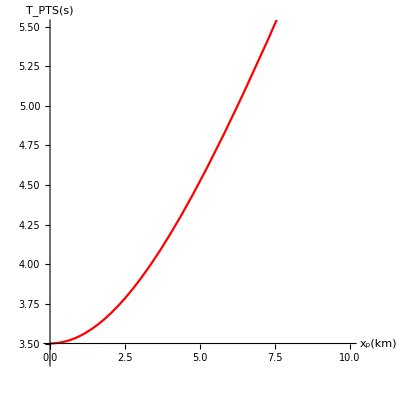

```mathematica
e1=ParametricPlot[{Xp,Tp},{p,0,0.9},AxesLabel->{Style["x_p(km)",FontSize->15],Style["T_PTS(s)",FontSize->15]},AspectRatio->1,PlotRange->{{0,10},{3.4,5.5}},PlotStyle->Red]
```

```mathematica
Xp0=Sum[(p veln1^2 *0.001)/(vel1(1-2 ET1 p^2 veln1^2)^(3/2) √(1-(1+2 ET1) p^2 veln1^2))/.param,{z,0,6,0.001}];
```

```mathematica
Tp0=Sum[(0.001*((1-2 ET1 p^2 veln1^2)^2+2ET1*p^4veln1^4))/(vel1(1-2 ET1 p^2 veln1^2)^(3/2) √(1-(1+2 ET1) p^2 veln1^2))/.param,{z,0,6,0.001}];
```

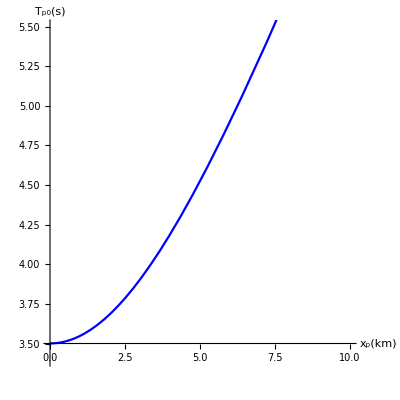

```mathematica
e2=ParametricPlot[{Xp0,Tp0},{p,0,0.9},AxesLabel->{Style["x_p(km)",FontSize->15],Style["T_p0(s)",FontSize->15]},AspectRatio->1,PlotRange->{{0,10},{3.4,5.5}},PlotStyle->Blue]
```

```mathematica
DTp=Abs[(Tp0-Tp)];
```

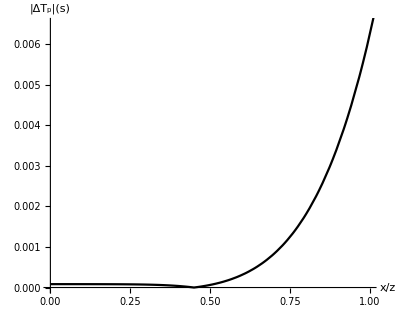

```mathematica
ParametricPlot[{Xp/6,DTp},{p,0,0.9},PlotRange->{{0,1},{0,0.0065}},PlotStyle->Black,AspectRatio->0.8,AxesLabel->{Style["x/z",FontSize->15],Style["|ΔT_p|(s)",FontSize->15]}]
```